```mathematica
Manipulate[
Module[{t,S,L,w,r1,r2,h,Tb,k,m,T,base,RY,YG,GB,col,cgrad,rectangular,annular,temperature},
(*size stuff*)
t=0.0015;(*m*)
S=0.01;

(*rectangular*)
L:=length/1000;
w:=width/1000;

(*annular*)
r1=0.003;(*base radius*)
r2:=radius2/1000;(*fin radius*)

(*therm. data*)
h=35;(*W/m2/K*)
Tb=500;(*base temp.*)
k:=Which[
mat==1,14,(*s.steel*)
mat==2,60.5,(*carbon steel*)
mat==3,80.2,(*iron*)
mat==4,110,(*brass*)
mat==5,237,(*aluminum*)
mat==6,401,(*copper*)
mat==7,2300(*diamond*)
];(*W/m/K*)

m:=√((2*h)/(k*t));
T[x_]:=Tb*Cosh[m*(L-x)]/Cosh[m*L];

base=-0.005;
(*RY:=Table[RGBColor[1,i,0],{i,0,1,0.1}];
YG:=Table[RGBColor[1-j,1,0],{j,0.1,1,0.1}];
GB:=Table[RGBColor[0,1,k],{k,0.1,1,0.1}];

col:=Join[RY,YG,GB];
cgrad[x_]:=Blend[col,1-Rescale[T[x],{286.7,500}]];*)
cgrad[x_]:=ColorData["TemperatureMap"][Rescale[T[x],{286.7,500}]];

rectangular:=Show[
Graphics3D[{GrayLevel[0.5],Cuboid[{base,0,0},{0,w,2*S+t}]}],
RegionPlot3D[z<S+t,{x,0,L},{y,0,w},{z,S,S+t},Mesh->None,
ColorFunction->(cgrad[#1]&),ColorFunctionScaling->False]
];

annular:=Show[
Graphics3D[{GrayLevel[0.5],Cylinder[{{0,0,0},{0,0,2*S+t}},r1]}]
];

temperature:=Plot3D[T,{x,0,L},{y,0,w},Mesh->None,ColorFunction->Function[{x,y,z},ColorData["TemperatureMap"][Rescale[z,{286.7,500}]]],ColorFunctionScaling->False];

Show[Switch[fin,1,rectangular,2,annular,3,temperature],Boxed->False,ViewPoint->{2,-2,1},Lighting->"Neutral",ImageSize->{250,350},PlotLabel->T[L]]

],
Column[{
Control[{{fin,1,""},{1->" rectangular ",2->" annular ",3->" temperature "},Setter}],
Control[{{mat,1,"material:"},{1->"stainless steel",2->"carbon steel",3->"iron",4->"brass",5->"aluminum",6->"copper",7->"diamond"},PopupMenu}],
Style["fin measurements (mm)",Bold],
PaneSelector[{
1->Row[{
Control[{{length,10,"length"},5,20,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{width,20,"width"},20,50,1,Appearance->"Labeled",ImageSize->Small}]
}],
2->Control[{{radius2,10,"radius"},5,15,1,Appearance->"Labeled",ImageSize->Small}],
3->Row[{
Control[{{length,10,"length"},5,20,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{width,20,"width"},20,50,1,Appearance->"Labeled",ImageSize->Small}]
}]
},Dynamic@fin]
}]
]
```

```mathematica
Module[{f},
f:=0.5733*x^2-21.905*x+500;
(*Plot3D[f,{x,0,20},{y,0,20},Mesh->None,ColorFunction->Function[{x,y,z},RGBColor[1,1-Rescale[z,{291.2,500}],0]],ColorFunctionScaling->False]*)
Plot3D[f,{x,0,20},{y,0,20},Mesh->None,ColorFunction->Function[{x,y,z},ColorData["TemperatureMap"][Rescale[z,{291.2,500}]]],ColorFunctionScaling->False]
]
```

-Graphics3D-

```mathematica
(0.5733*x^2-21.905*x+500)/.x->20
```

291.22

```mathematica
Module[{f},
f:=0.5733*x^2-21.905*x+500;

RegionPlot3D[z<1,{x,0,20},{y,0,20},{z,0,1},Mesh->None,PlotRange->{{0,20},{0,20},{-5,5}},ColorFunction->Function[{f,x,y},ColorData["TemperatureMap"][Rescale[f,{291.2,500}]]],
ColorFunctionScaling->False]
]
```

-Graphics3D-

```mathematica
Module[{colors,grad},
colors:=Join[Table[RGBColor[1,i,0],{i,0,1,0.1}],Table[RGBColor[1,1,i],{i,0.1,1,0.1}]];
grad[x_]:=Blend[colors,x];

Plot3D[Exp[-x^2-y^2],{x,-2,2},{y,-2,2},ColorFunction->Function[{x,y,z},grad[z]]]
]
```

-Graphics3D-

```mathematica
Module[{T,RY,YG,GB,col,cgrad},
T[x_]:=0.5733*x^2-21.905*x+500;

(*col:=Join[Table[RGBColor[1,i,0],{i,0,1,0.1}],Table[RGBColor[1,1,i],{i,0.1,1,0.1}]];*)
RY:=Table[RGBColor[1,i,0],{i,0,1,0.1}];
YG:=Table[RGBColor[1-j,1,0],{j,0.1,1,0.1}];
GB:=Table[RGBColor[0,1,k],{k,0.1,1,0.1}];

col:=Join[RY,YG,GB];
cgrad[x_]:=Blend[col,Rescale[T[x],{T[0],T[20]}]];

RegionPlot3D[z<1,{x,0,20},{y,0,20},{z,0,1},Mesh->None,PlotRange->{{0,20},{0,20},{-5,5}},
ColorFunction->(cgrad[#1]&),
ColorFunctionScaling->False]
]
```

-Graphics3D-

```mathematica
Join[Table[RGBColor[1,i,0],{i,0,1,0.1}],Table[RGBColor[1,1,i],{i,0.1,1,0.1}]]
```

{RGBColor[1, 0., 0],RGBColor[1, 0.1, 0],RGBColor[1, 0.2, 0],RGBColor[1, 0.30000000000000004, 0],RGBColor[1, 0.4, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0.6000000000000001, 0],RGBColor[1, 0.7000000000000001, 0],RGBColor[1, 0.8, 0],RGBColor[1, 0.9, 0],RGBColor[1, 1., 0],RGBColor[1, 1, 0.1],RGBColor[1, 1, 0.2],RGBColor[1, 1, 0.30000000000000004],RGBColor[1, 1, 0.4],RGBColor[1, 1, 0.5],RGBColor[1, 1, 0.6],RGBColor[1, 1, 0.7000000000000001],RGBColor[1, 1, 0.8],RGBColor[1, 1, 0.9],RGBColor[1, 1, 1.]}


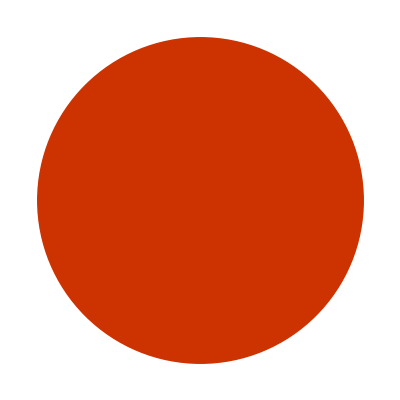
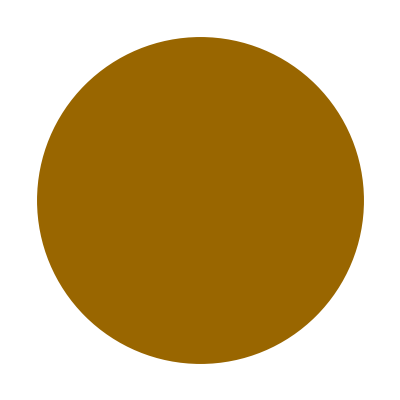
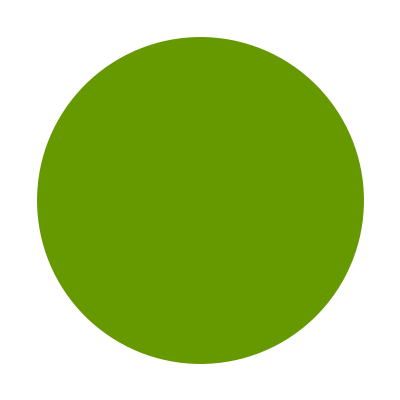
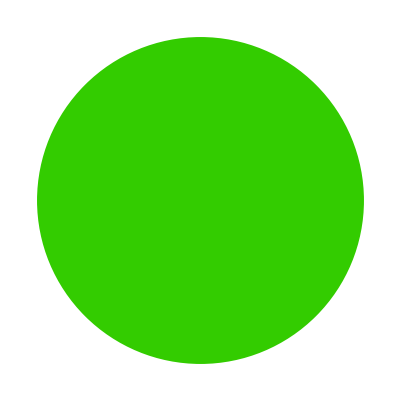
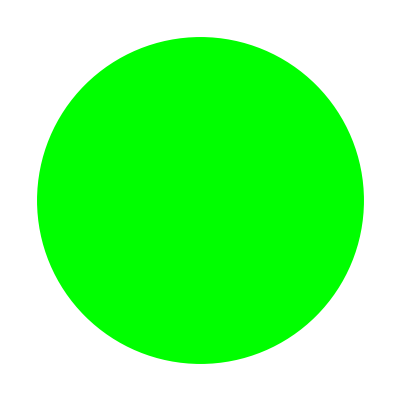

```mathematica
Table[Graphics[{RGBColor[1-i,i,0],Disk[]}],{i,0,1,0.2}]
```

```mathematica
Module[{RY,YG,GB},
RY:=Table[RGBColor[1,i,0],{i,0,1,0.1}];
YG:=Table[RGBColor[1-j,1,0],{j,0.1,1,0.1}];
GB:=Table[RGBColor[0,1,k],{k,0.1,1,0.1}];

Join[RY,YG,GB]
]
```

{RGBColor[1, 0., 0],RGBColor[1, 0.1, 0],RGBColor[1, 0.2, 0],RGBColor[1, 0.30000000000000004, 0],RGBColor[1, 0.4, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0.6000000000000001, 0],RGBColor[1, 0.7000000000000001, 0],RGBColor[1, 0.8, 0],RGBColor[1, 0.9, 0],RGBColor[1, 1., 0],RGBColor[0.9, 1, 0],RGBColor[0.8, 1, 0],RGBColor[0.7, 1, 0],RGBColor[0.6, 1, 0],RGBColor[0.5, 1, 0],RGBColor[0.4, 1, 0],RGBColor[0.29999999999999993, 1, 0],RGBColor[0.19999999999999996, 1, 0],RGBColor[0.09999999999999998, 1, 0],RGBColor[0., 1, 0],RGBColor[0, 1, 0.1],RGBColor[0, 1, 0.2],RGBColor[0, 1, 0.30000000000000004],RGBColor[0, 1, 0.4],RGBColor[0, 1, 0.5],RGBColor[0, 1, 0.6],RGBColor[0, 1, 0.7000000000000001],RGBColor[0, 1, 0.8],RGBColor[0, 1, 0.9],RGBColor[0, 1, 1.]}

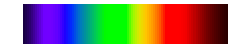

```mathematica
ColorData["VisibleSpectrum","Image"]
```

```mathematica
Module[{T,RY,YG,GB,col,cgrad},
T[x_]:=0.5733*x^2-21.905*x+500;

cgrad[x_]:=ColorData["VisibleSpectrum"][Rescale[T[x],{T[0],T[20]}]];

RegionPlot3D[z<1,{x,0,20},{y,0,20},{z,0,1},Mesh->None,PlotRange->{{0,20},{0,20},{-5,5}},
ColorFunction->(cgrad[#1]&),
ColorFunctionScaling->True]
]
```

-Graphics3D-